```mathematica
files = FileNames["*.tab"];
datas = Drop[Import[#], 1]&/@files;
ch1s=Transpose[{#[[All,1]],#[[All,2]]}]&/@datas;
ch2s=Transpose[{#[[All,1]],#[[All,3]]}]&/@datas;
data = Transpose[{ch1s, ch2s}];
```

```mathematica
fitdata = Table[Select[data[[i, 2]], #[[1]]≥ 0.0054 && #[[1]]≤0.015&], {i, 1, Length[data]}];
nlms = NonlinearModelFit[#, a - b ⅇ^(-c x), {a, b, c}, x]&/@fitdata;
```

```mathematica
funcs = Normal[#]&/@ nlms;
```

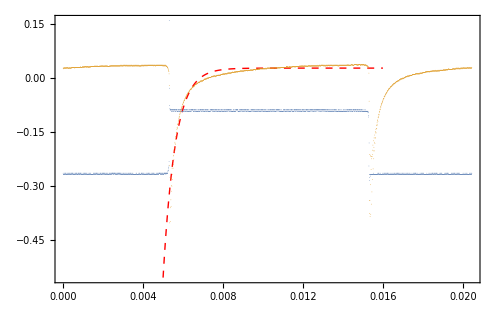
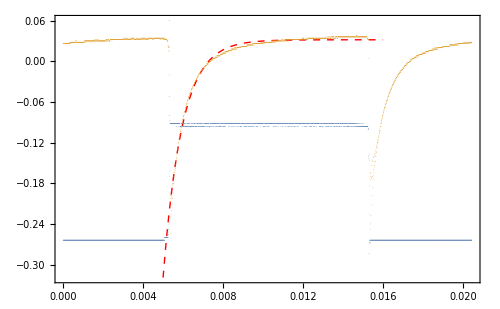
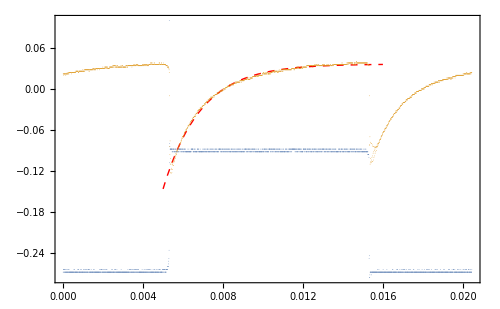
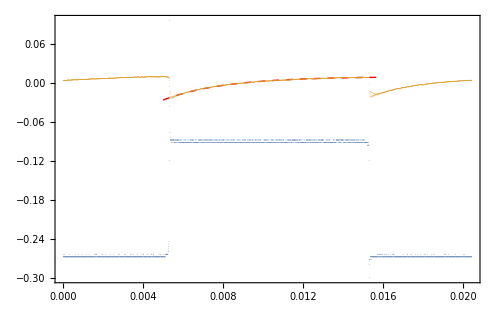
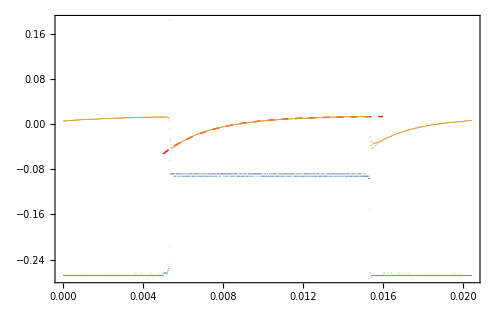
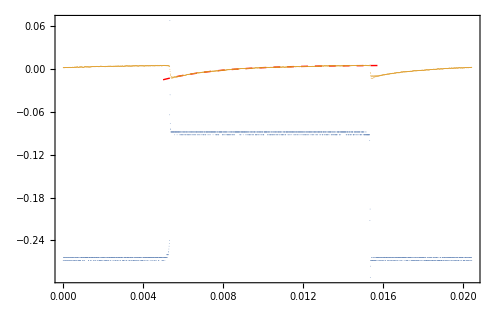
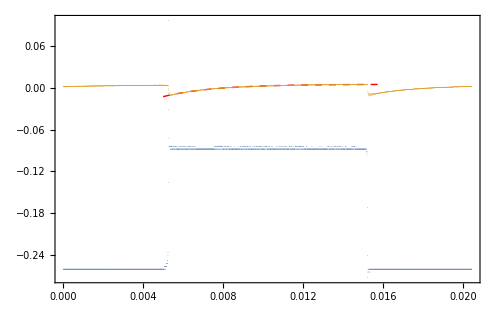
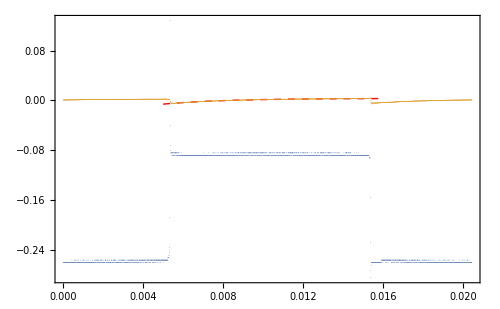

```mathematica
Show[Plot[#[[2]], {x, 0.005, 0.016},ImageSize->500, PlotRange->All, Frame->True, PlotStyle->{Red, Dashed, Thick}], ListPlot[#[[1]],PlotStyle->{PointSize[0.00001]}]]&/@ Transpose[{data, funcs}]
```

```mathematica
taus=#["ParameterTableEntries"][[3, 1]]&/@ nlms
```

{1646.12,1054.16,530.827,327.232,420.066,357.267,395.675,313.834,279.119}

```mathematica
filters = {0.,0.398736,0.453891,0.816374,1.04996,1.29003,1.49831,1.65801,2.06819}
```

{0.,0.398736,0.453891,0.816374,1.04996,1.29003,1.49831,1.65801,2.06819}

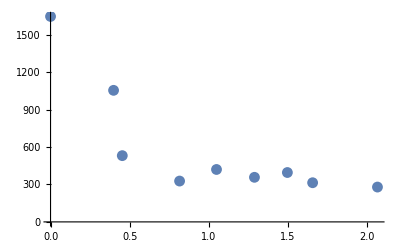

```mathematica
ListPlot[Transpose[{filters, taus}]]
```

```mathematica
taus2 = taus[[3 ;; ]];
filters2 = filters[[3;;]];
```

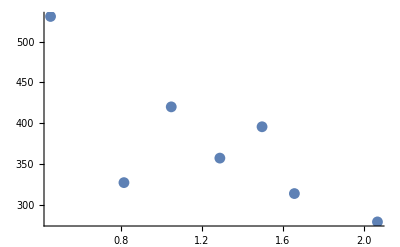

```mathematica
ListPlot[Transpose[{filters2, taus2}]]
```